Sculpin foraging pressure

Eden Forbes 2026

```mathematica
(* Fixed Parameters *)
a = 0.5; (* probability sculpin pursues *)
γ = 0.8; (* capture probability, assuming benthic invertebrate prey [0.1 for Mysis] *)

(* GLM fits *)
(* Movement distance *)
zM[size_]:= 19.336 + 0.1616 size 
(* Movement duration *)
sM[size_]:= 0.5375 + 0.0009 size 
(* Rest duration *)
sR[size_]:= 6.3906+ 0.0368 size 

(* Encounter rate *)
Aint[size_, d_]:= 2 d^2 ArcCos[zM[size]/(2 d)]-zM[size]/2 √(4 d^2-zM[size]^2);
eSCUL[size_, P_, d_]:= (P Pi d^2*(1-Aint[size, d]/(Pi d^2)))/(sM[size] + sR[size]);

(* Foraging pressure (type II) *)
p[size_, d_]:= (sM[size] + 2*sR[size]);
T2[size_, P_, d_]:=γ *(a eSCUL[size, P, d])/(1 + a eSCUL[size, P, d]*p[size, d]);
```

## Encounter rates

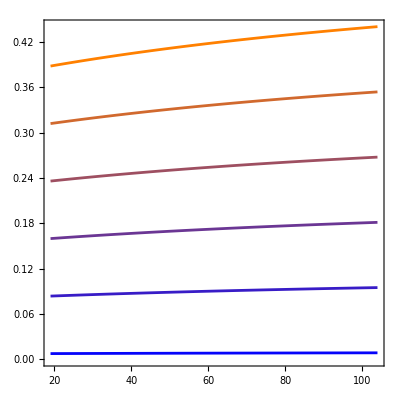

```mathematica
Plot[Evaluate@Table[Style[Re[eSCUL[size,dens,130]],Blend[{Blue,Orange},dens/0.0005]],{dens,0.00001,0.00051,0.0001}],{size,18.98,104}, AspectRatio->1, Frame->True,
LabelStyle->{Black,20}]
```

## Foraging pressure

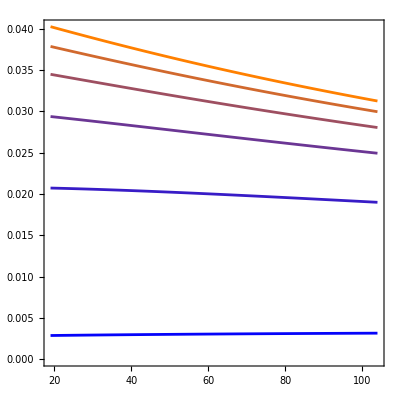

```mathematica
Plot[Evaluate@Table[Style[Re[T2[size,dens, 130]],Blend[{Blue,Orange},dens/0.0005]],{dens,0.00001,0.00051,0.0001}],{size,18.98,104}, AspectRatio->1, Frame->True,LabelStyle->{Black,20}]
```